```mathematica
Clear[x,y]; 
p=11;
Flatten[Table[ Solve[ {y^2== x^3-5 x + 3, x==u, Modulus==p}],{u, 0, p-1}] ,1]
```

{{Modulus→11,y→5,x→0},{Modulus→11,y→6,x→0},{Modulus→11,y→1,x→2},{Modulus→11,y→10,x→2},{Modulus→11,y→2,x→3},{Modulus→11,y→9,x→3},{Modulus→11,y→5,x→4},{Modulus→11,y→6,x→4},{Modulus→11,y→2,x→5},{Modulus→11,y→9,x→5},{Modulus→11,y→5,x→7},{Modulus→11,y→6,x→7},{Modulus→11,y→4,x→9},{Modulus→11,y→7,x→9}}

```mathematica
g1={x,y}/.Flatten[Table[ Solve[ {y^2== x^3-5 x + 3, x==u, Modulus==p}],{u, 0, p-1}] ,1]
```

{{0,5},{0,6},{2,1},{2,10},{3,2},{3,9},{4,5},{4,6},{5,2},{5,9},{7,5},{7,6},{9,4},{9,7}}

```mathematica
Mod[-5,11]
```

6

```mathematica
g2={x,y}/.Flatten[Table[ Solve[ {y^2== x^3+6 x + 3, x==u, Modulus==p}],{u, 0, p-1}] ,1]
```

{{0,5},{0,6},{2,1},{2,10},{3,2},{3,9},{4,5},{4,6},{5,2},{5,9},{7,5},{7,6},{9,4},{9,7}}

```mathematica
g1-g2
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

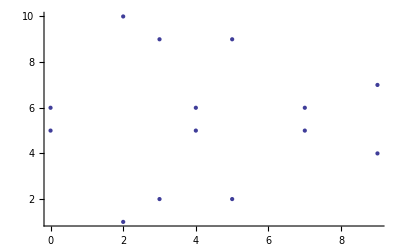

```mathematica
ListPlot[g1]
```

```mathematica
ListPlot3D[g1]
```

-Graphics3D-

```mathematica
ListPointPlot3D[g1]
```

-Graphics3D-